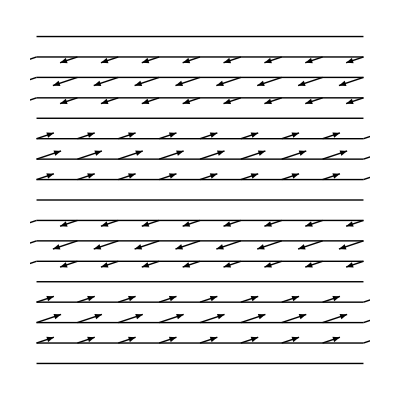

```mathematica
MovieFrame0=Join[Table[Line[{{-1,y},{1,y}}],{y,-10,3,1/8}],
Flatten[Table[Table[Arrow[{{x,y},{x,y}+.05Sin[2π y]{3,1}}],{x,-1,1,.25}],{y,-10,3,1/8}]]];
Graphics[MovieFrame0,PlotRange->{{-1,1},{0,2}}]
```

```mathematica
Clear[MovieFrame]
```

```mathematica
MovieFrame[t_]:=Map[#+{0,.1t}&,MovieFrame0,{3}]
```

#### Polarized plane wave. The horizontal lines are the wave fronts. They are planes seen edge-on. Each plane is a constant phase surface. The slanted lines are the vibrations. On a given phase surface they are all the same.

```mathematica
Animate[Graphics[MovieFrame[t],PlotRange->{{-1,1},{-.2,1.8}}],{t,0,1,.02}]
```

#### Strain for a polarized plane wave. uVec=(u1,u2,u3) is the vibration direction. The wave is moving in the nVec direction. nVec is bold n.

```mathematica
Clear[k ,x,y,z,ω,t,u1,u2,u3];
nVec={n1,n2,n3};  (* should be a unit vector *)
u={u1,u2,u3}Exp[I(k {x,y,z}.nVec-ω t)];   (* e.g., Fedorov's Eq 15.5, CHECK *)
```

```mathematica
D[u[[1]],z]
```

ⅈ ⅇ^(ⅈ (k (n1 x+n2 y+n3 z)-t ω)) k n3 u1

```mathematica
JacobianMatrix=({{D[u[[1]],x], D[u[[1]],y], D[u[[1]],z]}, {D[u[[2]],x], D[u[[2]],y], D[u[[2]],z]}, {D[u[[3]],x], D[u[[3]],y], D[u[[3]],z]}});  (* at (x,y,z) and time t *)
MatrixForm[Simplify[1/(k ⅈ Exp[I(k {x,y,z}.nVec-ω t)])JacobianMatrix]]
```

(n1 u1 | n2 u1 | n3 u1
n1 u2 | n2 u2 | n3 u2
n1 u3 | n2 u3 | n3 u3)

```mathematica
Print[Style["Strain at point ",16],Style["x",Bold,16],Style[" and time t is   ⅈk Exp[i(k{",16],Style["x·n",Bold,16],Style[" - ωt)]",16],MatrixForm[1/2(({{n1 u1, n2 u1, n3 u1}, {n1 u2, n2 u2, n3 u2}, {n1 u3, n2 u3, n3 u3}})+Transpose[({{n1 u1, n2 u1, n3 u1}, {n1 u2, n2 u2, n3 u2}, {n1 u3, n2 u3, n3 u3}})])]];
```

Strain at point x and time t is   ⅈk Exp[i(k{x·n - ωt)](n1 u1 | 1/2 (n2 u1+n1 u2) | 1/2 (n3 u1+n1 u3)
1/2 (n2 u1+n1 u2) | n2 u2 | 1/2 (n3 u2+n2 u3)
1/2 (n3 u1+n1 u3) | 1/2 (n3 u2+n2 u3) | n3 u3)

#### The strain is a beachball with λ2 = 0 and a fault plane perpendicular to the wave normal nVec. From its eigenvalues, the strain is obviously a double couple when (n1,n2,n3)·(u1,u2,u3)=0. When (u1,u2,u3)=t(n1,n2,n3) the eigenvalues have the form a, 0, 0.

```mathematica
Simplify[Eigenvalues[({{2 n1 u1, n2 u1+ n1 u2, n3 u1+ n1 u3}, {n2 u1+ n1 u2, 2n2 u2, n3 u2+ n2 u3}, {n3 u1+ n1 u3, n3 u2+ n2 u3, 2n3 u3}})]]
```

{0,n1 u1+n2 u2+n3 u3-√((n1^2+n2^2+n3^2) (u1^2+u2^2+u3^2)),n1 u1+n2 u2+n3 u3+√((n1^2+n2^2+n3^2) (u1^2+u2^2+u3^2))}

#### (ConstantStrain is no longer a unit matrix.)

```mathematica
ConstantStrain[{n1_,n2_,n3_},{u1_,u2_,u3_}]:=({{2 n1 u1, n2 u1+ n1 u2, n3 u1+ n1 u3}, {n2 u1+ n1 u2, 2 n2 u2, n3 u2+ n2 u3}, {n3 u1+ n1 u3, n3 u2+ n2 u3, 2 n3 u3}});
```

#### Framevisible has the frame vectors pointing toward us.

```mathematica
FrameVisible[M_,eye_]:=Select[{-Uraw[M],Uraw[M],Uraw[M].XRot[π],Uraw[M].YRot[π],Uraw[M].ZRot[π],
Uraw[M].xref,Uraw[M].yref,Uraw[M].zref},
     eye.(#.{1,0,0})≥0&&
eye.(#.{0,1,0})≥0&&
eye.(#.{0,0,1})≥0&][[1]];
```

```mathematica
Clear[GraphicsStrainMatrixForPlaneWave]
```

```mathematica
Eigenvalues[Tmat][[1]]
```

5.

```mathematica
BBcoords[ConstantStrain[nVec,uVec2]]
```

{0.,0.,1.41421,0.,0.,0.}

```mathematica
Tmat.BBcoords[ConstantStrain[nVec,uVec2]]-Eigenvalues[Tmat][[4]] BBcoords[ConstantStrain[nVec,uVec2]]
```

{0.,0.,0.,0.,0.,0.}

```mathematica
Tmat.BBcoords[ConstantStrain[nVec,uVec2]]
```

{0.,0.,2.82843,0.,0.,0.}

```mathematica
IsEigenvectorOfTmat[M_,λ_,Tmat_]:=length[Tmat.BBcoords[M]-λ BBcoords[M]];
```

```mathematica
Clear[IsAnEigenvectorOfTmat]
```

```mathematica
uVec=uVec2;
```

```mathematica
Union[Round[Eigenvalues[Tmat],.000001]]
```

{1.,3.,4.,5.}

```mathematica
{1.0000000000000002,3.,3.0000000000000004,3.9999999999999996,4.,5.000000000000002}
```

```mathematica
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat]
```

n = {1,0,0}

u = {1.,0.,0.},  M = ConstantStrain[n,u]

M is not an eigenvector of Tmat

u = {0.,1.,0.},  M = ConstantStrain[n,u]

λ = 2.,  |T M - λ M| = 0.,  so  M IS an eigenvector of Tmat

u = {0.,0.,1.},  M = ConstantStrain[n,u]

λ = 1.,  |T M - λ M| = 0.,  so  M IS an eigenvector of Tmat

```mathematica
PrintIsConstantStrainAnEigenvectorOfTmat[nVec_,uVec_,Tmat_]:=(Print[Style["u",Bold,16]," = ",uVec,",  M = ConstantStrain[",Style["n,u",Bold,16],"]"];
IsAnEigenvector=False;
Do[
M=ConstantStrain[nVec,uVec];
λλ=Union[Round[Eigenvalues[Tmat],.000001]][[i]];
If[Chop[IsEigenvectorOfTmat[M,λλ,Tmat]]==0,IsAnEigenvector=True;
Print["λ = ",λλ,",  |T M - λ M| = ",IsEigenvectorOfTmat[M,λλ,Tmat],",  so  M IS an eigenvector of Tmat"]],{i,Length[Union[Round[Eigenvalues[Tmat],.000001]]]}];
If[!IsAnEigenvector,Print["M is NOT an eigenvector of Tmat"]])
```

```mathematica
PrintIsConstantStrainAnEigenvectorOfTmat[nVec_,uVec1_,uVec2_,uVec3_,Tmat_]:=(Print["(For above diagram)  " ,Style["n",Bold,16]," = ",nVec];
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,Tmat];
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec2,Tmat];
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec3,Tmat];)
```

```mathematica
GraphicsStrainMatrixForPlaneWave[nVecNotNormalized_,uVec_,eye_,ArrowScale_,tkns_,BBrad_,centerBB_]:={nVec=unit[nVecNotNormalized];
frame1=FrameVisible[ConstantStrain[nVec,uVec],eye].{1,0,0};
frame2=FrameVisible[ConstantStrain[nVec,uVec],eye].{0,1,0};
frame3=FrameVisible[ConstantStrain[nVec,uVec],eye].{0,0,1};
BeachballForM[UnitMatrix[ConstantStrain[nVec,uVec]],centerBB,BBrad],
If[IsCrackMatrix[ConstantStrain[nVec,uVec]],{Thickness[.7tkns],White,Line[centerBB+BBrad Transpose[vertical[ cAxis[ConstantStrain[nVec,uVec]]]].#&/@EquatorList]}],(* white equator *)
{Thickness[tkns],Line[ShortenLineForArrow[centerBB+#&/@{BBrad×uVec,If[Chop[length[uVec-nVec]]==0,2.2BBrad-2×.95ArrowScale,2.2BBrad]uVec},ArrowScale]]},(* iine for GREEN vibration vector uVec *)
{Green,Arrow3D[centerBB+2.2BBrad uVec,uVec,ArrowScale]}, (* arrow for GREEN vibration vector uVec *)
(* *) 
{Hue[.59],Arrow3D[centerBB+If[Chop[length[uVec-nVec]]==0,2.2BBrad-.95ArrowScale,2.2BBrad] nVec,nVec,ArrowScale]},(* arrow for BLUE nVec *)
If[Chop[length[uVec-nVec]]≠0,{Thickness[tkns],Line[ShortenLineForArrow[centerBB+#&/@{BBrad×nVec,2.2BBrad×nVec},ArrowScale]]}],(* iine for BLUE vector nVec if nVec ≠ uVec *)
(* *) 
{Hue[.13],  (* the YELLOW frame for the strain matrix *)
Arrow3D[centerBB+If[Chop[length[frame1-nVec]]==0,2.2BBrad-2×.95ArrowScale,2.2BBrad] frame1,frame1,ArrowScale],
Arrow3D[centerBB+If[Chop[length[frame2-nVec]]==0,2.2BBrad-2×.95ArrowScale,2.2BBrad] frame2,frame2,ArrowScale],
Arrow3D[centerBB+If[Chop[length[frame3-nVec]]==0,2.2BBrad-2×.95ArrowScale,2.2BBrad] frame3,frame3,ArrowScale]},
{Thickness[tkns],
If[Chop[length[frame1-nVec]]≠0,Line[centerBB+#&/@ShortenLineForArrow[{{0,0,0},2.2BBrad×frame1},ArrowScale]]],
If[Chop[length[frame2-nVec]]≠0,Line[centerBB+#&/@ShortenLineForArrow[{{0,0,0},2.2BBrad×frame2},ArrowScale]]],
If[Chop[length[frame3-nVec]]≠0,Line[centerBB+#&/@ShortenLineForArrow[{{0,0,0},2.2BBrad×frame3},ArrowScale]]]}};
```

### Here is a typical strain matrix for a plane polarized wave.

```mathematica
ArrowScale=.2;tkns=.016;
nVec=xyztp[{40.,70}];
uVec1=xyztp[{55.,15}];
eye=30xyztp[{0,65}];
Print[Hue[.59],"   Wavefront normal"];
Print[Green,      "   Vibration direction"];
Print[Hue[.13],   "   Principal axes of strain"];
Graphics3D[GraphicsStrainMatrixForPlaneWave[nVec,uVec1,eye,ArrowScale,tkns,1,{0,0,0}],Lighting->"Neutral",Boxed->False,ViewPoint->eye,Lighting->"Neutral",Boxed->False,ImageSize->300]
```

Hue[0.59]   Wavefront normal

RGBColor[0, 1, 0]   Vibration direction

Hue[0.13]   Principal axes of strain

-Graphics3D-

```mathematica
MatrixForm[Simplify[6CmatOfTmat[TmatFor180]]]
```

(3 d+e+2 (f-√3 j+√2 k-√6 p) | -3 d+e+2 (f+√2 k) | -2 e+2 f+2 √3 j-√2 k-√6 p | 0 | 0 | -3 i+√3 o+√6 s
-3 d+e+2 (f+√2 k) | 3 d+e+2 (f+√3 j+√2 k+√6 p) | -2 e+2 f-2 √3 j-√2 k+√6 p | 0 | 0 | 3 i+√3 o+√6 s
-2 e+2 f+2 √3 j-√2 k-√6 p | -2 e+2 f-2 √3 j-√2 k+√6 p | 2 (2 e+f-2 √2 k) | 0 | 0 | -2 √3 o+√6 s
0 | 0 | 0 | 3 a | 3 g | 0
0 | 0 | 0 | 3 g | 3 b | 0
-3 i+√3 o+√6 s | 3 i+√3 o+√6 s | -2 √3 o+√6 s | 0 | 0 | 3 c)

```mathematica
TmatTest=Simplify[CmatOfTmat[TmatFor180]];
MatrixForm[TmatTest]
```

(1/6 (3 d+e+2 (f-√3 j+√2 k-√6 p)) | 1/6 (-3 d+e+2 (f+√2 k)) | 1/6 (-2 e+2 f+2 √3 j-√2 k-√6 p) | 0 | 0 | 1/6 (-3 i+√3 o+√6 s)
1/6 (-3 d+e+2 (f+√2 k)) | 1/6 (3 d+e+2 (f+√3 j+√2 k+√6 p)) | 1/6 (-2 e+2 f-2 √3 j-√2 k+√6 p) | 0 | 0 | 1/6 (3 i+√3 o+√6 s)
1/6 (-2 e+2 f+2 √3 j-√2 k-√6 p) | 1/6 (-2 e+2 f-2 √3 j-√2 k+√6 p) | 1/3 (2 e+f-2 √2 k) | 0 | 0 | -o/(√3)+s/(√6)
0 | 0 | 0 | a/2 | g/2 | 0
0 | 0 | 0 | g/2 | b/2 | 0
1/6 (-3 i+√3 o+√6 s) | 1/6 (3 i+√3 o+√6 s) | -o/(√3)+s/(√6) | 0 | 0 | c/2)

```mathematica
MatrixForm[TmatTest/.{
1/6 (3 d+e+2 (f-√3 j+√2 k-√6 p))->C11,
1/6 (3 d+e+2 (f+√3 j+√2 k+√6 p))->C22,
1/3 (2 e+f-2 √2 k)->C33,
a/2->C44,
b/2->C55,
c/2->C66,
1/6 (-3 d+e+2 (f+√2 k))->C12,
1/6 (-2 e+2 f+2 √3 j-√2 k-√6 p)->C13,
1/6 (-3 i+√3 o+√6 s)->C16,
1/6 (-2 e+2 f-2 √3 j-√2 k+√6 p)->C23,
1/6 (3 i+√3 o+√6 s)->C26,
-o/(√3)+s/(√6)->C36,
g/2->C45}]
```

(C11 | C12 | C13 | 0 | 0 | C16
C12 | C22 | C23 | 0 | 0 | C26
C13 | C23 | C33 | 0 | 0 | C36
0 | 0 | 0 | C44 | C45 | 0
0 | 0 | 0 | C45 | C55 | 0
C16 | C26 | C36 | 0 | 0 | C66)

```mathematica
MatrixForm[ChristoffelMatrix[{0,0,1},({{C11, C12, C13, 0, 0, C16}, {C12, C22, C23, 0, 0, C26}, {C13, C23, C33, 0, 0, C36}, {0, 0, 0, C44, C45, 0}, {0, 0, 0, C45, C55, 0}, {C16, C26, C36, 0, 0, C66}})]]
```

(C55 | C45 | 0
C45 | C44 | 0
0 | 0 | C33)

```mathematica
MatrixForm[Simplify[Eigensystem[({{C55, C45, 0}, {C45, C44, 0}, {0, 0, C33}})]]]
```

(C33 | 1/2 (C44+C55-√(C44^2+4 C45^2-2 C44 C55+C55^2)) | 1/2 (C44+C55+√(C44^2+4 C45^2-2 C44 C55+C55^2))
{0,0,1} | {-(C44-C55+√(C44^2+4 C45^2-2 C44 C55+C55^2))/(2 C45),1,0} | {(-C44+C55+√(C44^2+4 C45^2-2 C44 C55+C55^2))/(2 C45),1,0})

```mathematica
({{C33, 1/2 (C44+C55-√(C44^2+4 C45^2-2 C44 C55+C55^2)), 1/2 (C44+C55+√(C44^2+4 C45^2-2 C44 C55+C55^2))}, {{0,0,1}, {-C44+C55-√(C44^2+4 C45^2-2 C44 C55+C55^2),2 C45,0}, {-C44+C55+√(C44^2+4 C45^2-2 C44 C55+C55^2),2 C45,0}}})
```

```mathematica
Simplify[(-C44+C55-√(C44^2+4 C45^2-2 C44 C55+C55^2))(-C44+C55+√(C44^2+4 C45^2-2 C44 C55+C55^2))+2 C45 2 C45]
```

0

```mathematica
MatrixForm[Eigensystem[({{1., 4, 0}, {4, 2, 0}, {0, 0, 3}})]]
```

(5.53113 | 3. | -2.53113
{0.661803,0.749678,0.} | {0.,0.,1.} | {0.749678,-0.661803,0.})

#### But the elastic map needs to be positive definite, so you can’t just make up C11, C12, etc.

```mathematica
ArrowScale=.15;tkns=.009;
```

```mathematica
Clear[EigenvalueText]
```

```mathematica
cAxis[M_]:=Select[Table[{Eigenvalues[M][[i]],Eigenvectors[M][[i]]},{i,3}],Length[ListComplement[Eigenvalues[M],{#[[1]]}]]==2&][[1,2]];  (* needs to be checked *)
IsCrackMatrix[M_]:=Length[Union[Round[Eigenvalues[M],.000001]]]==2;
BlueGreenCoincide:=Chop[Min[length[uVec1-nVec],length[uVec2-nVec],length[uVec3-nVec]]]==0.;
EigenvalueTextForStrain[M_]:=If[Chop[Total[Eigenvalues[M]]]==0&&Chop[Eigenvalues[M][[1]]Eigenvalues[M][[2]]Eigenvalues[M][[3]]]==0,"    Double couple",PaddedForm[Chop[Eigenvalues[M]],{3,2}]];  (* for strain matrices *)
uVecText[uVec_]:=If[Chop[length[uVec-nVec]]==0,Style["n",Bold,16],PaddedForm[uVec,{3,2}]];
```

#### SymbolicOnly

```mathematica
ChristoffelPictureSymbolic[Tmat_,nVecNotNormalized_]:=(nVec=unit[nVecNotNormalized];
ChrisMat=Simplify[ChristoffelMatrix[nVec,CmatOfTmat[Tmat]]];
uVec1=Eigenvectors[ChrisMat][[1]];
uVec2=Eigenvectors[ChrisMat][[2]];
uVec3=Eigenvectors[ChrisMat][[3]];
Print[Style["n",Bold,16],If[length[nVecNotNormalized]≠1," = 1/(| |)"," = "],nVecNotNormalized,"  (wavefront normal vector)"];
Print["The Christoffel matrix for ",Style["n",Bold,16]," is ",MatrixForm[ChrisMat]]; 
Print["Eigensystem of Christoffel for ",Style["n",Bold,16]," is ",MatrixForm[Simplify[Eigensystem[ChrisMat]]],"   ",MatrixForm[{If[IsCrackMatrix[ChrisMat],"Uniaxial","Not uniaxial"],If[Chop[length[Cross[nVec,uVec1]]length[Cross[nVec,uVec2]]length[Cross[nVec,uVec3]]]==0,"There is a P-wave","There is no P-wave"]}]];
Print["The eigenvalue triples for the strain matrices are:"];
Print[ColumnForm[{
EigenvalueTextForStrain[ConstantStrain[nVec,uVec1]],
EigenvalueTextForStrain[ConstantStrain[nVec,uVec2]],
EigenvalueTextForStrain[ConstantStrain[nVec,uVec3]]}]];)
```

#### Numerical

```mathematica
ChristoffelPictureNumerical[Tmat_,nVecNotNormalized_,WantGraphics_]:=(nVec=unit[nVecNotNormalized];
ChrisMat=Simplify[ChristoffelMatrix[nVec,CmatOfTmat[Tmat]]];
uVec1=FrameVisible[ChrisMat,eye].{1,0,0};
uVec2=FrameVisible[ChrisMat,eye].{0,1,0};
uVec3=FrameVisible[ChrisMat,eye].{0,0,1};
centerXYZ={0,2+2.5Max[uVec1.unit[Cross[{0,0,1},eye]],uVec2.unit[Cross[{0,0,1},eye]],uVec3.unit[Cross[{0,0,1},eye]]],0};
Print[""];
Print["(For next diagram)  ",Style["n",Bold,16],If[length[nVecNotNormalized]≠1," = 1/(| |)"," = "],nVecNotNormalized,"  (wavefront normal vector)"];
Print["The Christoffel matrix for ",Style["n",Bold,16]," is ",MatrixForm[Round[ChrisMat,.01]]]; 
Print["Eigensystem of Christoffel for ",Style["n",Bold,16]," is ",MatrixForm[Round[Eigensystem[ChrisMat],.01]],"   ",MatrixForm[{If[IsCrackMatrix[ChrisMat],"Uniaxial","Not uniaxial"],If[Chop[length[Cross[nVec,uVec1]]length[Cross[nVec,uVec2]]length[Cross[nVec,uVec3]]]==0,"There is a P-wave","There is no P-wave"]}]];
Print["The eigenvalue triples for the strain matrices are:"];
Print[ColumnForm[{
EigenvalueTextForStrain[ConstantStrain[nVec,uVec1]],
EigenvalueTextForStrain[ConstantStrain[nVec,uVec2]],
EigenvalueTextForStrain[ConstantStrain[nVec,uVec3]]}],
ColumnForm[ {
SequenceForm["  for  ",Style["u1",Bold,14]," = "],
SequenceForm["  for  ",Style["u2",Bold,14]," = "],
SequenceForm["  for  ",Style["u3",Bold,14]," = "]}],
ColumnForm[{uVecText[uVec1],uVecText[uVec2],uVecText[uVec3]}],
ColumnForm[{SequenceForm[",  i.e.,  (θ, ϕ) = ",PaddedForm[IntegerPart[#],2]&/@{theta[uVec1],phi[uVec1]}],
                      SequenceForm[",  i.e.,  (θ, ϕ) = ",PaddedForm[IntegerPart[#],2]&/@{theta[uVec2],phi[uVec2]}],
                      SequenceForm[",  i.e.,  (θ, ϕ) = ",PaddedForm[IntegerPart[#],2]&/@{theta[uVec3],phi[uVec3]}]}]];
If[WantGraphics=="WantGraphics",Graphics3D[{
GraphicsStrainMatrixForPlaneWave[nVec,uVec1,eye,.8ArrowScale,.8tkns,BBrad,2.5uVec1],
GraphicsStrainMatrixForPlaneWave[nVec,uVec2,eye,.8ArrowScale,.8tkns,BBrad,2.5uVec2],
GraphicsStrainMatrixForPlaneWave[nVec,uVec3,eye,.8ArrowScale,.8tkns,BBrad,2.5uVec3],
If[GraphicsForSolid[centerXYZ]≠{},{
Text[Style["x",16],centerXYZ+{1,0,0}],
Text[Style["y",16],centerXYZ+{0,.9,0}],
Text[Style["z",16],centerXYZ+{0,0,lengthZ+.2}],
{Thickness[tkns],Line[centerXYZ+#&/@ShortenLineForArrow[{TailPt×nVec,1.2×lengthZ×nVec},ArrowScale]]},      (* line for BLUE normal nVec on SOLID *)
{Hue[.59],Arrow3D[centerXYZ+1.2×lengthZ×nVec,nVec,ArrowScale]}, (* BLUE arrow for SOLID *)}],
GraphicsForSolid[centerXYZ],
{Hue[.59],Polygon[Transpose[vertical[nVec]].ZRot[#].{.15,0,.35}&/@Range[0,2π,.05π]]},  (* BLUE disk *)
(**)
{Green,  (* GREEN arrow in XYZ *)
Arrow3D[uVec1,uVec1,ArrowScale],
Arrow3D[uVec2,uVec2,ArrowScale],
Arrow3D[uVec3,uVec3,ArrowScale]},
{Hue[.59],Arrow3D[If[BlueGreenCoincide,1-.95ArrowScale,1]nVec,nVec,ArrowScale]},(* BLUE arrow in XYZ *)
{Thickness[tkns],          (* lines for GREEN vibration vectors uVec at origin*) 
If[Chop[length[uVec1-nVec]]≠0,Line[ShortenLineForArrow[{{0,0,0},uVec1},ArrowScale]]],
If[Chop[length[uVec2-nVec]]≠0,Line[ShortenLineForArrow[{{0,0,0},uVec2},ArrowScale]]],
If[Chop[length[uVec3-nVec]]≠0,Line[ShortenLineForArrow[{{0,0,0},uVec3},ArrowScale]]]},
{Thickness[tkns],Line[ShortenLineForArrow[{{0,0,0},  If[BlueGreenCoincide,1-.8ArrowScale,1]nVec},ArrowScale]]}, (* line for BLUE arrow *)
(**)
{Green,If[IsCrackMatrix[ChrisMat],
{EdgeForm[],Polygon/@Map[Transpose[vertical[cAxis[ChrisMat]]].({{.5, 0, 0}, {0, .5, 0}, {0, 0, .025}}).#&,CylinderPolys,{2}]},
Polygon/@Map[.1Uraw[ChrisMat].#&,CubeFacePolys,{2}]]}},Lighting->"Neutral",ImageSize->If[GraphicsForSolid[centerXYZ]≠{},900,700],ViewPoint->eye,Boxed->False]]);
```

```mathematica
PrintChristoffelDataNumerical[Tmat_]:=(
Print["[T]_𝔹𝔹 =                 ",MatrixForm[Round[Tmat,.01]]];
Print["Voigt matrix C for T is ",MatrixForm[Round[CmatOfTmat[Tmat],.01]]];
Print[Hue[.59],"   ","Wavefront normal ",Style["n",Bold,16]];
Print[Green,       "   ", "Vibration directions ",Style["u1,u2,u3",Bold,15]];
Print[Hue[.13],              "   Principal axes of strain matrix"]);
```

```mathematica
PrintChristoffelDataSymbolic[Tmat_]:=(
Print["[T]_𝔹𝔹 =                 ",MatrixForm[Tmat]];
Print["Voigt matrix C for T is ",MatrixForm[Simplify[CmatOfTmat[Tmat]]]];
Print[Hue[.59],"   ","Wavefront normal ",Style["n",Bold,16]];
Print[Green,       "   ", "Vibration directions ",Style["u1,u2,u3",Bold,15]];
Print[Hue[.13],              "   Principal axes of strain matrix"]);
```

```mathematica
PrintChristoffelDataNumerical[Tmat]
```

[T]_𝔹𝔹 =                 (4. | 0. | 0. | 0. | 0. | 0.
0. | 4. | 0. | 0. | 0. | 0.
0. | 0. | 2. | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0.
0. | 0. | 0. | 0. | 0.9 | 0.17
0. | 0. | 0. | 0. | 0.17 | 0.7)

Voigt matrix C for T is (1.46 | -0.54 | -0.11 | 0. | 0. | 0.
-0.54 | 1.46 | -0.11 | 0. | 0. | 0.
-0.11 | -0.11 | 0.67 | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0.
0. | 0. | 0. | 0. | 2. | 0.
0. | 0. | 0. | 0. | 0. | 1.)

Hue[0.59]   Wavefront normal n

RGBColor[0, 1, 0]   Vibration directions u1,u2,u3

Hue[0.13]   Principal axes of strain matrix

#### The eigenvectors of the Christoffel matrix are the vibration directions. The eigenvalues determine the wave speeds. (λ = ρv^2) The blue disk is parallel to the wavefronts. The green disk signifies that all radial vectors in its plane are vibration directions.

#### A transverse isotropic example. Here, for n = (0,0,1) the P-wave is slower than the S-wave.

```mathematica
eye=50xyztp[{15,65}];
BBrad=.45;tkns=.005;ArrowScale=.16;lengthZ=.7;
Tmat=TmatFromEigensystem[{4,4,2,2,1,.6},basisBBprime[30.Degree]];  (* XISO *)
GraphicsForSolid[centerXYZ_]:={{EdgeForm[],FaceForm[{GrayLevel[.7]}],Polygon/@Map[centerXYZ+.2#&,CylinderPolys,{2}]},
{Thickness[.8tkns],
Line[centerXYZ+#&/@{{.2,   0,0},{.75,0,0}}],
Line[centerXYZ+#&/@{{0,.2,0},{0,.75,0}}],
Line[centerXYZ+#&/@{{0,  0,0},{0,0,lengthZ}}]}};
PrintChristoffelDataNumerical[Tmat];
nVecNotNormalized={0,0,1};TailPt=0;
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat]
nVecNotNormalized={1,0,0};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat]
nVecNotNormalized={1,1,3};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat]
```

[T]_𝔹𝔹 =                 (4. | 0. | 0. | 0. | 0. | 0.
0. | 4. | 0. | 0. | 0. | 0.
0. | 0. | 2. | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0.
0. | 0. | 0. | 0. | 0.9 | 0.17
0. | 0. | 0. | 0. | 0.17 | 0.7)

Voigt matrix C for T is (1.46 | -0.54 | -0.11 | 0. | 0. | 0.
-0.54 | 1.46 | -0.11 | 0. | 0. | 0.
-0.11 | -0.11 | 0.67 | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0.
0. | 0. | 0. | 0. | 2. | 0.
0. | 0. | 0. | 0. | 0. | 1.)

Hue[0.59]   Wavefront normal n

RGBColor[0, 1, 0]   Vibration directions u1,u2,u3

Hue[0.13]   Principal axes of strain matrix

n = {0,0,1}  (wavefront normal vector)

The Christoffel matrix for n is (2. | 0. | 0.
0. | 2. | 0.
0. | 0. | 0.67)

Eigensystem of Christoffel for n is (2. | 2. | 0.67
{0.,1.,0.} | {1.,0.,0.} | {0.,0.,1.})   (Uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

Double couple
    Double couple
{ 2.00, 0.00, 0.00}  for  u1 = 
  for  u2 = 
  for  u3 = { 1.00, 0.00, 0.00}
{ 0.00, 1.00, 0.00}
n,  i.e.,  (θ, ϕ) = {  0, 90}
,  i.e.,  (θ, ϕ) = { 90, 90}
,  i.e.,  (θ, ϕ) = {  0,  0}

-Graphics3D-

n = {0,0,1}

u = {1.,0.,0.},  M = ConstantStrain[n,u]

λ = 4.,  |T M - λ M| = 0.,  so  M IS an eigenvector of Tmat

u = {0.,1.,0.},  M = ConstantStrain[n,u]

λ = 4.,  |T M - λ M| = 0.,  so  M IS an eigenvector of Tmat

u = {0.,0.,1.},  M = ConstantStrain[n,u]

M is not an eigenvector of Tmat

n = {1,0,0}  (wavefront normal vector)

The Christoffel matrix for n is (1.46 | 0. | 0.
0. | 1. | 0.
0. | 0. | 2.)

Eigensystem of Christoffel for n is (2. | 1.46 | 1.
{0.,0.,1.} | {1.,0.,0.} | {0.,1.,0.})   (Not uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

Double couple
{ 2.00, 0.00, 0.00}
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = { 0.00, 0.00, 1.00}
n
{ 0.00, 1.00, 0.00},  i.e.,  (θ, ϕ) = {  0,  0}
,  i.e.,  (θ, ϕ) = {  0, 90}
,  i.e.,  (θ, ϕ) = { 90, 90}

-Graphics3D-

n = {1,0,0}

u = {0.,0.,1.},  M = ConstantStrain[n,u]

λ = 4.,  |T M - λ M| = 0.,  so  M IS an eigenvector of Tmat

u = {1.,0.,0.},  M = ConstantStrain[n,u]

M is not an eigenvector of Tmat

u = {0.,1.,0.},  M = ConstantStrain[n,u]

λ = 2.,  |T M - λ M| = 0.,  so  M IS an eigenvector of Tmat

n = 1/(| |){1,1,3}  (wavefront normal vector)

The Christoffel matrix for n is (1.86 | 0.04 | 0.52
0.04 | 1.86 | 0.52
0.52 | 0.52 | 0.91)

Eigensystem of Christoffel for n is (2.29 | 1.82 | 0.53
{-0.62,-0.62,-0.47} | {0.71,-0.71,0.} | {-0.33,-0.33,0.88})   (Not uniaxial
There is no P-wave)

The eigenvalue triples for the strain matrices are:

{ 1.80,-0.20, 0.00}
    Double couple
{ 1.60,-0.40, 0.00}  for  u1 = 
  for  u2 = 
  for  u3 = { 0.62, 0.62, 0.47}
{ 0.71,-0.71, 4.06×10^-17}
{-0.33,-0.33, 0.88},  i.e.,  (θ, ϕ) = { 45, 62}
,  i.e.,  (θ, ϕ) = {-44, 90}
,  i.e.,  (θ, ϕ) = {-135, 27}

-Graphics3D-

n = {1/(√11),1/(√11),3/(√11)}

u = {0.62482,0.62482,0.468187},  M = ConstantStrain[n,u]

M is not an eigenvector of Tmat

u = {0.707107,-0.707107,4.05854×10^-17},  M = ConstantStrain[n,u]

M is not an eigenvector of Tmat

u = {-0.331058,-0.331058,0.883629},  M = ConstantStrain[n,u]

M is not an eigenvector of Tmat

#### A cubic example.

```mathematica
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat];
```

(For above diagram)  n = {1/(√2),0,1/(√2)}

u = {0.707107,0.,0.707107},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {0.707107,0.,-0.707107},  M = ConstantStrain[n,u]

λ = 2.,  |T M - λ M| = 5.14789×10^-16,  so  M IS an eigenvector of Tmat

u = {0.,1.,0.},  M = ConstantStrain[n,u]

λ = 1.,  |T M - λ M| = 0.,  so  M IS an eigenvector of Tmat

```mathematica
eye=50xyztp[{15,65}];
BBrad=.45;tkns=.005;lengthZ=.75;
Tmat=TmatFromEigensystem[{1.,1,1,2,2,3},basisBB];  (* CUBIC *)
GraphicsForSolid[centerXYZ_]:={{GrayLevel[.7],Polygon/@Map[centerXYZ+.2#&,CubeFacePolys,{2}]},
{Thickness[.8tkns],
Line[centerXYZ+#&/@{{.2,   0,0},{.75,0,0}}],
Line[centerXYZ+#&/@{{0,.2,0},{0,.75,0}}],
Line[centerXYZ+#&/@{{0,  0,0},{0,0,lengthZ}}]}};
PrintChristoffelDataNumerical[Tmat];
nVecNotNormalized={0,0,1};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat];
nVecNotNormalized={1,1,1};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat];
nVecNotNormalized={1,0,1};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat];
```

[T]_𝔹𝔹 =                 (1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0.
0. | 0. | 0. | 0. | 2. | 0.
0. | 0. | 0. | 0. | 0. | 3.)

Voigt matrix C for T is (2.33 | 0.33 | 0.33 | 0. | 0. | 0.
0.33 | 2.33 | 0.33 | 0. | 0. | 0.
0.33 | 0.33 | 2.33 | 0. | 0. | 0.
0. | 0. | 0. | 0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0.5)

Hue[0.59]   Wavefront normal n

RGBColor[0, 1, 0]   Vibration directions u1,u2,u3

Hue[0.13]   Principal axes of strain matrix

n = {0,0,1}  (wavefront normal vector)

The Christoffel matrix for n is (0.5 | 0. | 0.
0. | 0.5 | 0.
0. | 0. | 2.33)

Eigensystem of Christoffel for n is (2.33 | 0.5 | 0.5
{0.,0.,1.} | {1.,0.,0.} | {0.,1.,0.})   (Uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00, 0.00, 0.00}
    Double couple
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = n
{ 1.00, 0.00, 0.00}
{ 0.00, 1.00, 0.00},  i.e.,  (θ, ϕ) = {  0,  0}
,  i.e.,  (θ, ϕ) = {  0, 90}
,  i.e.,  (θ, ϕ) = { 90, 90}

-Graphics3D-

(For above diagram)  n = {0,0,1}

u = {0.,0.,1.},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {1.,0.,0.},  M = ConstantStrain[n,u]

λ = 1.,  |T M - λ M| = 0.,  so  M IS an eigenvector of Tmat

u = {0.,1.,0.},  M = ConstantStrain[n,u]

λ = 1.,  |T M - λ M| = 0.,  so  M IS an eigenvector of Tmat

n = 1/(| |){1,1,1}  (wavefront normal vector)

The Christoffel matrix for n is (1.11 | 0.28 | 0.28
0.28 | 1.11 | 0.28
0.28 | 0.28 | 1.11)

Eigensystem of Christoffel for n is (1.67 | 0.83 | 0.83
{-0.58,-0.58,-0.58} | {-0.41,-0.41,0.82} | {0.71,-0.71,0.})   (Uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00, 0.00, 0.00}
    Double couple
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = n
{ 0.41, 0.41,-0.82}
{ 0.71,-0.71, 0.00},  i.e.,  (θ, ϕ) = { 44, 54}
,  i.e.,  (θ, ϕ) = { 44, 144}
,  i.e.,  (θ, ϕ) = {-45, 90}

-Graphics3D-

(For above diagram)  n = {1/(√3),1/(√3),1/(√3)}

u = {0.57735,0.57735,0.57735},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {0.408248,0.408248,-0.816497},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {0.707107,-0.707107,0.},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

n = 1/(| |){1,0,1}  (wavefront normal vector)

The Christoffel matrix for n is (1.42 | 0. | 0.42
0. | 0.5 | 0.
0.42 | 0. | 1.42)

Eigensystem of Christoffel for n is (1.83 | 1. | 0.5
{-0.71,0.,-0.71} | {-0.71,0.,0.71} | {0.,-1.,0.})   (Not uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00, 0.00, 0.00}
    Double couple
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = n
{ 0.71, 0.00,-0.71}
{ 0.00, 1.00, 0.00},  i.e.,  (θ, ϕ) = {  0, 44}
,  i.e.,  (θ, ϕ) = {  0, 135}
,  i.e.,  (θ, ϕ) = { 90, 90}

-Graphics3D-

(For above diagram)  n = {1/(√2),0,1/(√2)}

u = {0.707107,0.,0.707107},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {0.707107,0.,-0.707107},  M = ConstantStrain[n,u]

λ = 2.,  |T M - λ M| = 5.14789×10^-16,  so  M IS an eigenvector of Tmat

u = {0.,1.,0.},  M = ConstantStrain[n,u]

λ = 1.,  |T M - λ M| = 0.,  so  M IS an eigenvector of Tmat

#### A monoclinic example. Note the P-wave is not fastest.

```mathematica
r=30Degree;
eye=50xyztp[{15,65}];
BBrad=.45;tkns=.005;
Tmat=TmatFromEigensystem[.1{20,18,3,14,5,16},UprightBasisForMono[r]];  (* monoclinic *)
GraphicsForSolid[centerXYZ_]:={{GrayLevel[.7],Polygon/@Map[centerXYZ+{0,0,.2}+.4ZRot[-r].#&,wedgePolys,{2}]},
 {Thickness[.8tkns],
Line[centerXYZ+#&/@{{.2,   0,0},{.7,0,0}}],
Line[centerXYZ+#&/@{{0,.2,0},{0,.7,0}}],
Line[centerXYZ+#&/@{{0,  0,0},{0,0,.7}}]}};
PrintChristoffelDataNumerical[Tmat];
Print["r = ",r,"  (θ = -r and θ = -r + π/2 give the two S-wave polarizations for "Style["n",Bold,14]," = (0,0,1))"];
nVecNotNormalized={0,0,1};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat];
nVecNotNormalized={1,0,0};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat];
nVecNotNormalized={3,0,-1};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat];
```

[T]_𝔹𝔹 =                 (1.95 | 0.09 | 0. | 0. | 0. | 0.
0.09 | 1.85 | 0. | 0. | 0. | 0.
0. | 0. | 0.95 | 0.23 | -0.22 | -0.47
0. | 0. | 0.23 | 1.34 | -0.08 | 0.13
0. | 0. | -0.22 | -0.08 | 0.37 | 0.16
0. | 0. | -0.47 | 0.13 | 0.16 | 1.15)

Voigt matrix C for T is (1.13 | -0.15 | 0.12 | 0. | 0. | -0.37
-0.15 | 1.24 | 0.32 | 0. | 0. | -0.14
0.12 | 0.32 | 0.48 | 0. | 0. | -0.07
0. | 0. | 0. | 0.97 | 0.04 | 0.
0. | 0. | 0. | 0.04 | 0.92 | 0.
-0.37 | -0.14 | -0.07 | 0. | 0. | 0.47)

Hue[0.59]   Wavefront normal n

RGBColor[0, 1, 0]   Vibration directions u1,u2,u3

Hue[0.13]   Principal axes of strain matrix

r = 30 °  (θ = -r and θ = -r + π/2 give the two S-wave polarizations for  n = (0,0,1))

n = {0,0,1}  (wavefront normal vector)

The Christoffel matrix for n is (0.92 | 0.04 | 0.
0.04 | 0.97 | 0.
0. | 0. | 0.48)

Eigensystem of Christoffel for n is (1. | 0.9 | 0.48
{0.5,0.87,0.} | {0.87,-0.5,0.} | {0.,0.,1.})   (Not uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

Double couple
    Double couple
{ 2.00, 0.00, 0.00}  for  u1 = 
  for  u2 = 
  for  u3 = { 0.50, 0.87, 0.00}
{ 0.87,-0.50, 0.00}
n,  i.e.,  (θ, ϕ) = { 60, 90}
,  i.e.,  (θ, ϕ) = {-30, 90}
,  i.e.,  (θ, ϕ) = {  0,  0}

-Graphics3D-

n = {1,0,0}  (wavefront normal vector)

The Christoffel matrix for n is (1.13 | -0.37 | 0.
-0.37 | 0.47 | 0.
0. | 0. | 0.92)

Eigensystem of Christoffel for n is (1.29 | 0.92 | 0.31
{0.91,-0.41,0.} | {0.,0.,1.} | {0.41,0.91,0.})   (Not uniaxial
There is no P-wave)

The eigenvalue triples for the strain matrices are:

{ 1.91,-0.09, 0.00}
    Double couple
{ 1.41,-0.59, 0.00}  for  u1 = 
  for  u2 = 
  for  u3 = { 0.91,-0.41, 0.00}
{ 0.00, 0.00, 1.00}
{ 0.41, 0.91, 0.00},  i.e.,  (θ, ϕ) = {-24, 90}
,  i.e.,  (θ, ϕ) = {  0,  0}
,  i.e.,  (θ, ϕ) = { 65, 90}

-Graphics3D-

n = 1/(| |){3,0,-1}  (wavefront normal vector)

The Christoffel matrix for n is (1.11 | -0.33 | -0.31
-0.33 | 0.52 | 0.01
-0.31 | 0.01 | 0.88)

Eigensystem of Christoffel for n is (1.42 | 0.75 | 0.34
{0.82,-0.3,-0.49} | {0.33,-0.45,0.83} | {0.47,0.84,0.26})   (Not uniaxial
There is no P-wave)

The eigenvalue triples for the strain matrices are:

{ 1.93,-0.07, 0.00}
{ 1.05,-0.95, 0.00}
{ 1.36,-0.64, 0.00}  for  u1 = 
  for  u2 = 
  for  u3 = { 0.82,-0.30,-0.49}
{ 0.33,-0.45, 0.83}
{ 0.47, 0.84, 0.26},  i.e.,  (θ, ϕ) = {-20, 119}
,  i.e.,  (θ, ϕ) = {-53, 33}
,  i.e.,  (θ, ϕ) = { 60, 74}

-Graphics3D-

#### A tetragonal example.

```mathematica
eye=50xyztp[{15,65}];lengthZ=.7;
Tmat=TmatFromEigensystem[{1,1,2,5,4,3},basisBB90[0,50.Degree]];  (* TET *)
GraphicsForSolid[centerXYZ_]:={{GrayLevel[.7],Polygon/@Map[centerXYZ+.6#&,SquarePrismPolys,{2}]},
{Thickness[.8tkns],
Line[centerXYZ+#&/@{{.2,   0,0},{.7,0,0}}],
Line[centerXYZ+#&/@{{0,.2,0},{0,.7,0}}],
Line[centerXYZ+#&/@{{0,  0,0},{0,0,lengthZ}}]}};
PrintChristoffelDataNumerical[Tmat];
nVecNotNormalized={0,0,1};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
nVecNotNormalized={1,0,0};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
nVecNotNormalized={Cos[π/8],Sin[π/8],0};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
nVecNotNormalized={3,0,-1};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
```

[T]_𝔹𝔹 =                 (1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 2. | 0. | 0. | 0.
0. | 0. | 0. | 5. | 0. | 0.
0. | 0. | 0. | 0. | 3.41 | 0.49
0. | 0. | 0. | 0. | 0.49 | 3.59)

Voigt matrix C for T is (4.5 | -0.5 | -0.06 | 0. | 0. | 0.
-0.5 | 4.5 | -0.06 | 0. | 0. | 0.
-0.06 | -0.06 | 3.01 | 0. | 0. | 0.
0. | 0. | 0. | 0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0.5 | 0.
0. | 0. | 0. | 0. | 0. | 1.)

Hue[0.59]   Wavefront normal n

RGBColor[0, 1, 0]   Vibration directions u1,u2,u3

Hue[0.13]   Principal axes of strain matrix

n = {0,0,1}  (wavefront normal vector)

The Christoffel matrix for n is (0.5 | 0. | 0.
0. | 0.5 | 0.
0. | 0. | 3.01)

Eigensystem of Christoffel for n is (3.01 | 0.5 | 0.5
{0.,0.,1.} | {1.,0.,0.} | {0.,1.,0.})   (Uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00, 0.00, 0.00}
    Double couple
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = n
{ 1.00, 0.00, 0.00}
{ 0.00, 1.00, 0.00},  i.e.,  (θ, ϕ) = {  0,  0}
,  i.e.,  (θ, ϕ) = {  0, 90}
,  i.e.,  (θ, ϕ) = { 90, 90}

-Graphics3D-

n = {1,0,0}  (wavefront normal vector)

The Christoffel matrix for n is (4.5 | 0. | 0.
0. | 1. | 0.
0. | 0. | 0.5)

Eigensystem of Christoffel for n is (4.5 | 1. | 0.5
{1.,0.,0.} | {0.,1.,0.} | {0.,0.,1.})   (Not uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00, 0.00, 0.00}
    Double couple
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = n
{ 0.00, 1.00, 0.00}
{ 0.00, 0.00, 1.00},  i.e.,  (θ, ϕ) = {  0, 90}
,  i.e.,  (θ, ϕ) = { 90, 90}
,  i.e.,  (θ, ϕ) = {  0,  0}

-Graphics3D-

nIf[√(Cos[π/8]^2+Sin[π/8]^2)≠1, = 1/(| |), = ]{Cos[π/8],Sin[π/8],0}  (wavefront normal vector)

The Christoffel matrix for n is (3.98 | 0.18 | 0.
0.18 | 1.51 | 0.
0. | 0. | 0.5)

Eigensystem of Christoffel for n is (4. | 1.5 | 0.5
{1.,0.07,0.} | {-0.07,1.,0.} | {0.,0.,1.})   (Not uniaxial
There is no P-wave)

The eigenvalue triples for the strain matrices are:

{ 1.95,-0.05, 0.00}
{ 1.32,-0.68, 0.00}
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = { 1.00, 0.07, 0.00}
{-0.07, 1.00, 0.00}
{ 0.00, 0.00, 1.00},  i.e.,  (θ, ϕ) = {  4, 90}
,  i.e.,  (θ, ϕ) = { 94, 90}
,  i.e.,  (θ, ϕ) = {  0,  0}

-Graphics3D-

n = 1/(| |){3,0,-1}  (wavefront normal vector)

The Christoffel matrix for n is (4.1 | 0. | -0.13
0. | 0.95 | 0.
-0.13 | 0. | 0.75)

Eigensystem of Christoffel for n is (4.1 | 0.95 | 0.75
{1.,0.,-0.04} | {0.,1.,0.} | {0.04,0.,1.})   (Not uniaxial
There is no P-wave)

The eigenvalue triples for the strain matrices are:

{ 1.96,-0.04, 0.00}
    Double couple
{-1.28, 0.72, 0.00}  for  u1 = 
  for  u2 = 
  for  u3 = { 1.00,-1.11×10^-16,-0.04}
{ 1.11×10^-16, 1.00,-3.43×10^-21}
{ 0.04,-4.39×10^-18, 1.00},  i.e.,  (θ, ϕ) = {  0, 92}
,  i.e.,  (θ, ϕ) = { 90, 90}
,  i.e.,  (θ, ϕ) = {  0,  2}

-Graphics3D-

#### An isotropic example.

```mathematica
eye=50xyztp[{15,65}];lengthZ=.7;
Tmat=TmatFromEigensystem[{1.,1,1,1,1,2},basisBB];  (* ISO *)
GraphicsForSolid[centerXYZ_]:={{EdgeForm[],FaceForm[GrayLevel[.7]],Polygon/@Map[centerXYZ+.25#&,SpherePolyList[1,0,360,0,180,15,15],{2}]},
{Thickness[.8tkns],
Line[centerXYZ+#&/@{{.25,   0,0},{.7,0,0}}],
Line[centerXYZ+#&/@{{0,.25,0},{0,.7,0}}],
Line[centerXYZ+#&/@{{0,  0,.25},{0,0,lengthZ}}]}};
PrintChristoffelDataNumerical[Tmat];
nVecNotNormalized={2.,-1,3};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
```

[T]_𝔹𝔹 =                 (1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 2.)

Voigt matrix C for T is (1.33 | 0.33 | 0.33 | 0. | 0. | 0.
0.33 | 1.33 | 0.33 | 0. | 0. | 0.
0.33 | 0.33 | 1.33 | 0. | 0. | 0.
0. | 0. | 0. | 0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0.5)

Hue[0.59]   Wavefront normal n

RGBColor[0, 1, 0]   Vibration directions u1,u2,u3

Hue[0.13]   Principal axes of strain matrix

n = 1/(| |){2.,-1,3}  (wavefront normal vector)

The Christoffel matrix for n is (0.74 | -0.12 | 0.36
-0.12 | 0.56 | -0.18
0.36 | -0.18 | 1.04)

Eigensystem of Christoffel for n is (1.33 | 0.5 | 0.5
{0.53,-0.27,0.8} | {0.72,-0.36,-0.6} | {0.45,0.89,0.})   (Uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00, 0.00, 0.00}
    Double couple
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = n
{ 0.72,-0.36,-0.60}
{ 0.45, 0.89, 0.00},  i.e.,  (θ, ϕ) = {-26, 36}
,  i.e.,  (θ, ϕ) = {-26, 126}
,  i.e.,  (θ, ϕ) = { 63, 90}

-Graphics3D-

```mathematica
nVecNotNormalized={0,0,1};TailPt=0;
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"noWantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat]
```

(For next diagram)  n = {0,0,1}  (wavefront normal vector)

The Christoffel matrix for n is (1.52 | 0. | 0.
0. | 1.52 | 0.
0. | 0. | 2.3)

Eigensystem of Christoffel for n is (2.3 | 1.52 | 1.52
{0.,0.,1.} | {1.,0.,0.} | {0.,1.,0.})   (Uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00, 0.00, 0.00}
    Double couple
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = n
{ 1.00, 0.00, 0.00}
{ 0.00, 1.00, 0.00},  i.e.,  (θ, ϕ) = {  0,  0}
,  i.e.,  (θ, ϕ) = {  0, 90}
,  i.e.,  (θ, ϕ) = { 90, 90}

(For above diagram)  n = {0,0,1}

u = {0.,0.,1.},  M = ConstantStrain[n,u]

λ = 1.,  |T M - λ M| = 4.55832,  so  M IS an eigenvector of Tmat

λ = 3.,  |T M - λ M| = 4.,  so  M IS an eigenvector of Tmat

λ = 4.,  |T M - λ M| = 5.06072,  so  M IS an eigenvector of Tmat

λ = 5.,  |T M - λ M| = 6.57432,  so  M IS an eigenvector of Tmat

u = {1.,0.,0.},  M = ConstantStrain[n,u]

λ = 1.,  |T M - λ M| = 2.88124,  so  M IS an eigenvector of Tmat

λ = 3.,  |T M - λ M| = 0.245576,  so  M IS an eigenvector of Tmat

λ = 4.,  |T M - λ M| = 1.39273,  so  M IS an eigenvector of Tmat

λ = 5.,  |T M - λ M| = 2.79626,  so  M IS an eigenvector of Tmat

u = {0.,1.,0.},  M = ConstantStrain[n,u]

λ = 1.,  |T M - λ M| = 2.88124,  so  M IS an eigenvector of Tmat

λ = 3.,  |T M - λ M| = 0.245576,  so  M IS an eigenvector of Tmat

λ = 4.,  |T M - λ M| = 1.39273,  so  M IS an eigenvector of Tmat

λ = 5.,  |T M - λ M| = 2.79626,  so  M IS an eigenvector of Tmat

#### A trigonal example

```mathematica
eye=50xyztp[{15,65}];
BBrad=.45;tkns=.004;ArrowScale=.16;lengthZ=.7;
Tmat=TmatFromEigensystem[{3,3,4,4,5,1},basisBB120[20.Degree,28Degree,0]];  (* TRIG *)
Clear[GraphicsForSolid];
GraphicsForSolid[centerXYZ_]:={{Thickness[.8tkns],
Line[centerXYZ+#&/@{{0,   0,0},{.7,0,0}}],
Line[centerXYZ+#&/@{{0,.3,0},{0,.75,0}}],
Line[centerXYZ+#&/@{{0,  0,0},{0,0,lengthZ}}]},
{GrayLevel[.7],Polygon/@Map[centerXYZ+.3#&,TriangularPrismPolys,{2}]}};
PrintChristoffelDataNumerical[Tmat];
nVecNotNormalized={0,0,1};TailPt=0;
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat]
nVecNotNormalized={0,1,0};  TailPt=.3;
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat]
nVecNotNormalized={1,0,0};TailPt=0;
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat]
nVecNotNormalized={3,1,-2};
ChristoffelPictureNumerical[Tmat,nVecNotNormalized,"WantGraphics"]
PrintIsConstantStrainAnEigenvectorOfTmat[nVec,uVec1,uVec2,uVec3,Tmat]
```

[T]_𝔹𝔹 =                 (3.22 | 0. | -0.41 | 0. | 0. | 0.
0. | 3.22 | 0. | -0.41 | 0. | 0.
-0.41 | 0. | 3.78 | 0. | 0. | 0.
0. | -0.41 | 0. | 3.78 | 0. | 0.
0. | 0. | 0. | 0. | 4.53 | 1.29
0. | 0. | 0. | 0. | 1.29 | 1.47)

Voigt matrix C for T is (3.74 | -0.04 | -1.32 | 0. | 0.21 | 0.
-0.04 | 3.74 | -1.32 | 0. | -0.21 | 0.
-1.32 | -1.32 | 2.3 | 0. | 0. | 0.
0. | 0. | 0. | 1.61 | 0. | -0.21
0.21 | -0.21 | 0. | 0. | 1.61 | 0.
0. | 0. | 0. | -0.21 | 0. | 1.89)

Hue[0.59]   Wavefront normal n

RGBColor[0, 1, 0]   Vibration directions u1,u2,u3

Hue[0.13]   Principal axes of strain matrix

(For next diagram)  n = {0,0,1}  (wavefront normal vector)

The Christoffel matrix for n is (1.61 | 0. | 0.
0. | 1.61 | 0.
0. | 0. | 2.3)

Eigensystem of Christoffel for n is (2.3 | 1.61 | 1.61
{0.,0.,1.} | {1.,0.,0.} | {0.,1.,0.})   (Uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00, 0.00, 0.00}
    Double couple
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = n
{ 1.00, 0.00, 0.00}
{ 0.00, 1.00, 0.00},  i.e.,  (θ, ϕ) = {  0,  0}
,  i.e.,  (θ, ϕ) = {  0, 90}
,  i.e.,  (θ, ϕ) = { 90, 90}

-Graphics3D-

(For above diagram)  n = {0,0,1}

u = {0.,0.,1.},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {1.,0.,0.},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {0.,1.,0.},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

(For next diagram)  n = {0,1,0}  (wavefront normal vector)

The Christoffel matrix for n is (1.89 | 0. | -0.21
0. | 3.74 | 0.
-0.21 | 0. | 1.61)

Eigensystem of Christoffel for n is (3.74 | 2. | 1.5
{0.,1.,0.} | {0.88,0.,-0.47} | {0.47,0.,0.88})   (Not uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00, 0.00, 0.00}
    Double couple
    Double couple  for  u1 = 
  for  u2 = 
  for  u3 = n
{ 0.88, 0.00,-0.47}
{ 0.47, 0.00, 0.88},  i.e.,  (θ, ϕ) = { 90, 90}
,  i.e.,  (θ, ϕ) = {  0, 117}
,  i.e.,  (θ, ϕ) = {  0, 27}

-Graphics3D-

(For above diagram)  n = {0,1,0}

u = {0.,1.,0.},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {0.882948,0.,-0.469472},  M = ConstantStrain[n,u]

λ = 4.,  |T M - λ M| = 9.93014×10^-16,  so  M IS an eigenvector of Tmat

u = {0.469472,0.,0.882948},  M = ConstantStrain[n,u]

λ = 3.,  |T M - λ M| = 4.44089×10^-16,  so  M IS an eigenvector of Tmat

(For next diagram)  n = {1,0,0}  (wavefront normal vector)

The Christoffel matrix for n is (3.74 | 0. | 0.21
0. | 1.89 | 0.
0.21 | 0. | 1.61)

Eigensystem of Christoffel for n is (3.76 | 1.89 | 1.59
{-1.,0.,-0.1} | {0.,-1.,0.} | {-0.1,0.,1.})   (Not uniaxial
There is no P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00,-0.00, 0.00}
    Double couple
{-1.10, 0.90, 0.00}  for  u1 = 
  for  u2 = 
  for  u3 = { 1.00, 0.00, 0.10}
{ 0.00, 1.00, 0.00}
{-0.10, 0.00, 1.00},  i.e.,  (θ, ϕ) = {  0, 84}
,  i.e.,  (θ, ϕ) = { 90, 90}
,  i.e.,  (θ, ϕ) = { 180,  5}

-Graphics3D-

(For above diagram)  n = {1,0,0}

u = {0.995387,0.,0.0959438},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {0.,1.,0.},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {-0.0959438,0.,0.995387},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

(For next diagram)  n = 1/(| |){3,1,-2}  (wavefront normal vector)

The Christoffel matrix for n is (2.82 | 0.46 | 0.
0.46 | 2.12 | -0.13
0. | -0.13 | 1.81)

Eigensystem of Christoffel for n is (3.05 | 1.97 | 1.73
{0.89,0.45,-0.05} | {0.39,-0.73,0.56} | {-0.21,0.52,0.83})   (Not uniaxial
There is no P-wave)

The eigenvalue triples for the strain matrices are:

{ 1.86,-0.14, 0.00}
{-1.18, 0.82, 0.00}
{-1.47, 0.53, 0.00}  for  u1 = 
  for  u2 = 
  for  u3 = { 0.89, 0.45,-0.05}
{ 0.39,-0.73, 0.56}
{-0.21, 0.52, 0.83},  i.e.,  (θ, ϕ) = { 26, 92}
,  i.e.,  (θ, ϕ) = {-61, 55}
,  i.e.,  (θ, ϕ) = { 112, 34}

-Graphics3D-

(For above diagram)  n = {3/(√14),1/(√14),-√(2/7)}

u = {0.894021,0.445295,-0.049387},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {0.394039,-0.729042,0.559671},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

u = {-0.213213,0.519818,0.827242},  M = ConstantStrain[n,u]

M is NOT an eigenvector of Tmat

#### ZRot[ξ] is assumed to be a non-trivial symmetry of the elastic map if and only if ξ = π. Next is the proof that the intrinsic parameter r in Eq 104 and Theorem 7 of the paper submitted March 2021 determines the S - wave vibration directions for plane waves moving along the z - axis. Specifically, the vibrations are horizontal with θ = -r and θ = -r +π/2. See the monoclinic example above..

```mathematica
Clear[r];MatrixForm[Simplify[ChristoffelMatrix[{0,0,1},CmatOfTmat[({{λ1 Cos[r]^2+λ2 Sin[r]^2, (λ1-λ2) Cos[r] Sin[r], 0, 0, 0, 0}, {(λ1-λ2) Cos[r] Sin[r], λ2 Cos[r]^2+λ1 Sin[r]^2, 0, 0, 0, 0}, {0, 0, c, i, o, s}, {0, 0, i, d, j, p}, {0, 0, o, j, e, k}, {0, 0, s, p, k, f}})]]]] 
MatrixForm[Simplify[Eigensystem[ChristoffelMatrix[{0,0,1},CmatOfTmat[({{λ1 Cos[r]^2+λ2 Sin[r]^2, (λ1-λ2) Cos[r] Sin[r], 0, 0, 0, 0}, {(λ1-λ2) Cos[r] Sin[r], λ2 Cos[r]^2+λ1 Sin[r]^2, 0, 0, 0, 0}, {0, 0, c, i, o, s}, {0, 0, i, d, j, p}, {0, 0, o, j, e, k}, {0, 0, s, p, k, f}})]]]]]
```

(1/2 (λ2 Cos[r]^2+λ1 Sin[r]^2) | 1/4 (λ1-λ2) Sin[2 r] | 0
1/4 (λ1-λ2) Sin[2 r] | 1/2 (λ1 Cos[r]^2+λ2 Sin[r]^2) | 0
0 | 0 | 1/3 (2 e+f-2 √2 k))

(1/3 (2 e+f-2 √2 k) | λ1/2 | λ2/2
{0,0,1} | {Tan[r],1,0} | {-Cot[r],1,0})

```mathematica
Clear[e,f,r,k,λ1,λ2];
({{1/3 (2 e+f-2 √2 k), λ1/2, λ2/2}, {{0,0,1}, {Sin[r],Cos[r],0}, {-Cos[r],Sin[r],0}}})==({{1/3 (2 e+f-2 √2 k), λ1/2, λ2/2}, {{0,0,1}, {Cos[-r+π/2],Sin[-r+π/2],0}, -{Cos[-r],Sin[-r],0}}})
```

True

```mathematica
Simplify[ChristoffelMatrix[{0,0,1},CmatOfTmat[({{λ1 Cos[r]^2+λ2 Sin[r]^2, (λ1-λ2) Cos[r] Sin[r], 0, 0, 0, 0}, {(λ1-λ2) Cos[r] Sin[r], λ2 Cos[r]^2+λ1 Sin[r]^2, 0, 0, 0, 0}, {0, 0, c, i, o, s}, {0, 0, i, d, j, p}, {0, 0, o, j, e, k}, {0, 0, s, p, k, f}})]].{Cos[-r],Sin[-r],0}==λ2/2{Cos[-r],Sin[-r],0}]
Simplify[ChristoffelMatrix[{0,0,1},CmatOfTmat[({{λ1 Cos[r]^2+λ2 Sin[r]^2, (λ1-λ2) Cos[r] Sin[r], 0, 0, 0, 0}, {(λ1-λ2) Cos[r] Sin[r], λ2 Cos[r]^2+λ1 Sin[r]^2, 0, 0, 0, 0}, {0, 0, c, i, o, s}, {0, 0, i, d, j, p}, {0, 0, o, j, e, k}, {0, 0, s, p, k, f}})]].{Cos[-r+π/2],Sin[-r+π/2],0}==λ1/2{Cos[-r+π/2],Sin[-r+π/2],0}]
```

True

True

## P-wave faster than S-wave for ISO

```mathematica
Print["[T]_𝔹𝔹 = "MatrixForm[TmatForISO],"  So a and f are the eigenvalues of [T]_𝔹𝔹. They are positive if T is stable."];
Print["The Christoffel matrix for n = (0,0,1) and T is ",MatrixForm[Simplify[ChristoffelMatrix[{0,0,1},CmatOfTmat[TmatForISO]]]]];
Print["Here the vibration directions (eigenvectors of the Christoffel matrix) and wave speeds are obvious from Christoffel. Thus for stable isotropic maps the P-wave is always faster than the S-wave."];
```

[T]_𝔹𝔹 =  (a | 0 | 0 | 0 | 0 | 0
0 | a | 0 | 0 | 0 | 0
0 | 0 | a | 0 | 0 | 0
0 | 0 | 0 | a | 0 | 0
0 | 0 | 0 | 0 | a | 0
0 | 0 | 0 | 0 | 0 | f)  So a and f are the eigenvalues of [T]_𝔹𝔹. They are positive if T is stable.

The Christoffel matrix for n = (0,0,1) and T is (a/2 | 0 | 0
0 | a/2 | 0
0 | 0 | 1/3 (2 a+f))

Here the vibration directions (eigenvectors of the Christoffel matrix) and wave speeds are obvious from Christoffel. Thus for stable isotropic maps the P-wave is always faster than the S-wave.

```mathematica
h0=1/2 ArcTan[√8,1];TmatXISO=Simplify[TmatFromEigensystem[{a,a,c,c,λ5,λ6},basisBBprime[t]]];
Print["[T]_𝔹𝔹 = "MatrixForm[TmatXISO]];
Print["Eigensystem of [T]_𝔹𝔹 is ",MatrixForm[Simplify[Eigensystem[TmatXISO]]]];
Print["Christoffel for n = (0,0,1) is ",MatrixForm[Simplify[ChristoffelMatrix[{0,0,1},CmatOfTmat[TmatXISO]]]],", independent of c."];
Print["The vibration directions and wave speeds are obvious from Christoffel. The P-wave and S-wave speeds are unrelated."];
Print[Simplify[ChristoffelMatrix[{0,0,1},CmatOfTmat[TmatXISO]]==1/2({{a, 0, 0}, {0, a, 0}, {0, 0, λ5 (1 -Sin[2(t-h0)])+λ6 (1 +Sin[2(t-h0)])}})]]
```

[T]_𝔹𝔹 =  (a | 0 | 0 | 0 | 0 | 0
0 | a | 0 | 0 | 0 | 0
0 | 0 | c | 0 | 0 | 0
0 | 0 | 0 | c | 0 | 0
0 | 0 | 0 | 0 | λ5 Cos[t]^2+λ6 Sin[t]^2 | (λ5-λ6) Cos[t] Sin[t]
0 | 0 | 0 | 0 | (λ5-λ6) Cos[t] Sin[t] | λ6 Cos[t]^2+λ5 Sin[t]^2)

Eigensystem of [T]_𝔹𝔹 is (a | a | c | c | λ5 | λ6
{0,1,0,0,0,0} | {1,0,0,0,0,0} | {0,0,0,1,0,0} | {0,0,1,0,0,0} | {0,0,0,0,Cot[t],1} | {0,0,0,0,-Tan[t],1})

Christoffel for n = (0,0,1) is (a/2 | 0 | 0
0 | a/2 | 0
0 | 0 | 1/6 (3 (λ5+λ6)+(λ5-λ6) Cos[2 t]-2 √2 (λ5-λ6) Sin[2 t])), independent of c.

The vibration directions and wave speeds are obvious from Christoffel. The P-wave and S-wave speeds are unrelated.

True

```mathematica
Simplify[1/6 (3 (λ5+λ6)+(λ5-λ6) Cos[2 t]-2 √2 (λ5-λ6) Sin[2 t])==λ5/6 (3 + Cos[2 t]-2 √2  Sin[2 t])+λ6/6 (3 - Cos[2 t]+2 √2  Sin[2 t])]
Simplify[1/6 (3 (λ5+λ6)+(λ5-λ6) Cos[2 t]-2 √2 (λ5-λ6) Sin[2 t])==λ5/2 (1 -Sin[2(t-h0)])+λ6/2 (1 +Sin[2(t-h0)])]
```

True

True

```mathematica
1.t0/Degree
```

54.7356

```mathematica
Simplify[Cos[2 t]-2 √2  Sin[2 t]==3(1/3 Cos[2 t]-(√8)/3  Sin[2 t])] 
Simplify[Cos[2 t]-2 √2  Sin[2 t]==3(Sin[2h0]Cos[2 t]-Cos[2h0]  Sin[2 t])]
Simplify[Cos[2 t]-2 √2  Sin[2 t]==-3Sin[2(t-h0)]]
```

True

True

True

```mathematica
h0=1/2 ArcTan[√8,1];
1.h0/Degree
Cos[2h0]
Sin[2h0]
Simplify[Cos[2 t]-2 √2  Sin[2 t]==-3Sin[2(t-h0)]]
```

9.73561

(2 √2)/3

1/3

True

λ1 = 10, λ3 = -1

Δa = 0.075

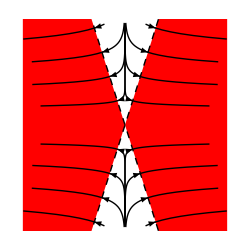

```mathematica
λ1=10;λ3=-1;Δa=.075;
Print["λ1 = ",λ1,", λ3 = ",λ3];
Print["Δa = ",Δa];
Graphics[{{Red,
Polygon[{{0,0},{-1,  √(-λ1/λ3)},{-1, - √(-λ1/λ3)}}],
Polygon[{{0,0},{1,  √(-λ1/λ3)},{1, - √(-λ1/λ3)}}]},
Table[{
Arrow[{a{√-λ3,  √λ1}-.01unit[{λ1 √-λ3,  λ3 √λ1}],a{√-λ3,  √λ1}}],
Arrow[{a{√-λ3,  -√λ1}-.01unit[{λ1 √-λ3, - λ3 √λ1}],a{√-λ3,  -√λ1}}],
Line[Select[a{√-λ3 Exp[λ1 #],  √λ1 Exp[λ3 #]}&/@Range[-2,2,.02],Abs[#[[1]]]<1&&Abs[#[[2]]]<1&]],
Line[Select[a{√-λ3 Exp[λ1 #],  -√λ1 Exp[λ3 #]}&/@Range[-2,2,.02],Abs[#[[1]]]<1&&Abs[#[[2]]]<1&]]},{a,Δa,1,Δa}],
Table[{
Arrow[{a{√-λ3,  √λ1}+.01unit[{λ1 √-λ3,  λ3 √λ1}],a{√-λ3,  √λ1}}],
Arrow[{a{√-λ3,  -√λ1}+.01unit[{λ1 √-λ3, - λ3 √λ1}],a{√-λ3,  -√λ1}}],
Line[Select[a{√-λ3 Exp[λ1 #],  √λ1 Exp[λ3 #]}&/@Range[-2,2,.02],Abs[#[[1]]]<1&&Abs[#[[2]]]<1&]],
Line[Select[a{√-λ3 Exp[λ1 #],  -√λ1 Exp[λ3 #]}&/@Range[-2,2,.02],Abs[#[[1]]]<1&&Abs[#[[2]]]<1&]]},{a,-Δa,-1,-Δa}],
{Dashing[{.02,.02}],
Line[{{-1,-√(-λ1/λ3)},{1,  √(-λ1/λ3)}}],
Line[{{-1,  √(-λ1/λ3)},{1,-√(-λ1/λ3)}}]}},PlotRange->{{-1,1},{-1,1}},ImageSize->250]
```

λ1 = 1, λ3 = -1

Δa = 0.25

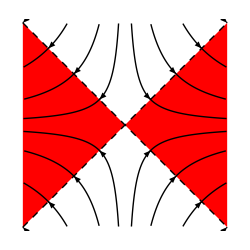

```mathematica
';
```

λ1 = 1, λ3 = -4.

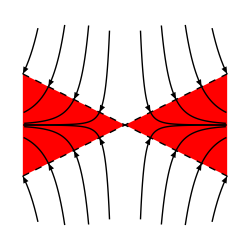

```mathematica
;lk
```

λ1 = 1, λ3 = -12

Δa = 0.0625

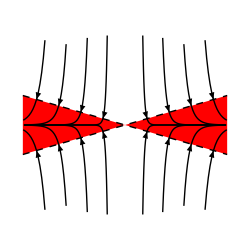

```mathematica
lkj
```

```mathematica
MatrixForm[TmatFor180]
```

(a | g | 0 | 0 | 0 | 0
g | b | 0 | 0 | 0 | 0
0 | 0 | c | i | o | s
0 | 0 | i | d | j | p
0 | 0 | o | j | e | 1
0 | 0 | s | p | 1 | f)

```mathematica
eye=50xyztp[{15,65}];
BBrad=.45;tkns=.005;
Tmat=TmatFor180;  (* monoclinic *)
nVecNotNormalized={0,0,1};
ChristoffelPictureSymbolic[Tmat,nVecNotNormalized]
```

n = {0,0,1}  (wavefront normal vector)

The Christoffel matrix for n is (b/2 | g/2 | 0
g/2 | a/2 | 0
0 | 0 | 1/3 (-2 √2+2 e+f))

Eigensystem of Christoffel for n is (1/3 (-2 √2+2 e+f) | 1/4 (a+b-√(a^2-2 a b+b^2+4 g^2)) | 1/4 (a+b+√(a^2-2 a b+b^2+4 g^2))
{0,0,1} | {-(a-b+√(a^2-2 a b+b^2+4 g^2))/(2 g),1,0} | {(-a+b+√(a^2-2 a b+b^2+4 g^2))/(2 g),1,0})   (Not uniaxial
There is a P-wave)

The eigenvalue triples for the strain matrices are:

{ 2.00, 0.00, 0.00}
    Double couple
    Double couple

## fff

```mathematica
Clear[u];
MatrixForm[TmatBlankSlate]
```

(a | g | m | q | t | v
g | b | h | n | r | u
m | h | c | i | o | s
q | n | i | d | j | p
t | r | o | j | e | 1
v | u | s | p | 1 | f)

```mathematica
eye=50xyztp[{15,65}];
BBrad=.45;tkns=.005;
Tmat=Simplify[TmatOfCmat[TmatBlankSlate]];  (* trivial symmetry *)
PrintChristoffelDataSymbolic[Tmat];
nVecNotNormalized={0,0,1};
ChristoffelPictureSymbolic[Tmat,nVecNotNormalized]
```

[T]_𝔹𝔹 =                 (2 d | 2 j | 2 p | n-q | (-2 i+n+q)/(√3) | √(2/3) (i+n+q)
2 j | 2 e | 2 | r-t | (-2 o+r+t)/(√3) | √(2/3) (o+r+t)
2 p | 2 | 2 f | u-v | (-2 s+u+v)/(√3) | √(2/3) (s+u+v)
n-q | r-t | u-v | 1/2 (a+b-2 g) | (-a+b-2 h+2 m)/(2 √3) | (-a+b+h-m)/(√6)
(-2 i+n+q)/(√3) | (-2 o+r+t)/(√3) | (-2 s+u+v)/(√3) | (-a+b-2 h+2 m)/(2 √3) | 1/6 (a+b+4 c+2 g-4 h-4 m) | (a+b-2 c+2 g-h-m)/(3 √2)
√(2/3) (i+n+q) | √(2/3) (o+r+t) | √(2/3) (s+u+v) | (-a+b+h-m)/(√6) | (a+b-2 c+2 g-h-m)/(3 √2) | 1/3 (a+b+c+2 g+2 h+2 m))

Voigt matrix C for T is (a | g | m | q | t | v
g | b | h | n | r | u
m | h | c | i | o | s
q | n | i | d | j | p
t | r | o | j | e | 1
v | u | s | p | 1 | f)

Hue[0.59]   Wavefront normal n

RGBColor[0, 1, 0]   Vibration directions u1,u2,u3

Hue[0.13]   Principal axes of strain matrix

n = {0,0,1}  (wavefront normal vector)

The Christoffel matrix for n is (e | j | o
j | d | i
o | i | c)

Eigensystem of Christoffel for n is (Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1] | Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2] | Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]
{(c d-i^2-(c+d) Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2)/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]),(-c j+i o+j Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1])/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]),1} | {(c d-i^2-(c+d) Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2)/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]),(-c j+i o+j Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2])/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]),1} | {(c d-i^2-(c+d) Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2)/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]),(-c j+i o+j Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3])/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]),1})   (Not uniaxial
If[√(((c j)/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1])-(i o)/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1])-(j Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1])/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]))^2+(-c/o+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]/o-i^2/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1])+(c i j)/(o (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]))-(i j Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1])/(o (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1])))^2) √(((c j)/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2])-(i o)/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2])-(j Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2])/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]))^2+(-c/o+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]/o-i^2/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2])+(c i j)/(o (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]))-(i j Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2])/(o (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2])))^2) √(((c j)/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3])-(i o)/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3])-(j Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3])/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]))^2+(-c/o+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]/o-i^2/(i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3])+(c i j)/(o (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]))-(i j Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3])/(o (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3])))^2)==0,There is a P-wave,There is no P-wave])

The eigenvalue triples for the strain matrices are:

If[(2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]-√((2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1])^2+4 (c^2 d^2-2 c d i^2+i^4+c^2 j^2-2 c i j o+i^2 o^2-2 c^2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]-2 c d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]+2 c i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]+2 d i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]-2 c j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]+2 i j o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]+c^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2+4 c d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2+d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2-2 i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2+j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2-2 c Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^3-2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^3+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^4)))/(2 (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]))+(2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]+√((2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1])^2+4 (c^2 d^2-2 c d i^2+i^4+c^2 j^2-2 c i j o+i^2 o^2-2 c^2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]-2 c d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]+2 c i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]+2 d i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]-2 c j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]+2 i j o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]+c^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2+4 c d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2+d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2-2 i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2+j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^2-2 c Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^3-2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^3+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]^4)))/(2 (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,1]))==0,    Double couple,Chop[Eigenvalues[{{ 0.00, 0.00,-(c-Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 1.00])/o+(i (c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 1.00]))/(o (i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 1.00]))},{ 0.00, 0.00,-(c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 1.00])/(i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 1.00])},{-(c-Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 1.00])/o+(i (c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 1.00]))/(o (i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 1.00])),-(c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 1.00])/(i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 1.00]), 2.00}}]]]
If[(2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]-√((2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2])^2+4 (c^2 d^2-2 c d i^2+i^4+c^2 j^2-2 c i j o+i^2 o^2-2 c^2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]-2 c d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]+2 c i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]+2 d i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]-2 c j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]+2 i j o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]+c^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2+4 c d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2+d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2-2 i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2+j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2-2 c Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^3-2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^3+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^4)))/(2 (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]))+(2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]+√((2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2])^2+4 (c^2 d^2-2 c d i^2+i^4+c^2 j^2-2 c i j o+i^2 o^2-2 c^2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]-2 c d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]+2 c i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]+2 d i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]-2 c j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]+2 i j o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]+c^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2+4 c d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2+d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2-2 i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2+j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^2-2 c Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^3-2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^3+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]^4)))/(2 (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,2]))==0,    Double couple,Chop[Eigenvalues[{{ 0.00, 0.00,-(c-Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 2.00])/o+(i (c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 2.00]))/(o (i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 2.00]))},{ 0.00, 0.00,-(c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 2.00])/(i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 2.00])},{-(c-Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 2.00])/o+(i (c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 2.00]))/(o (i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 2.00])),-(c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 2.00])/(i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 2.00]), 2.00}}]]]
If[(2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]-√((2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3])^2+4 (c^2 d^2-2 c d i^2+i^4+c^2 j^2-2 c i j o+i^2 o^2-2 c^2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]-2 c d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]+2 c i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]+2 d i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]-2 c j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]+2 i j o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]+c^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2+4 c d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2+d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2-2 i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2+j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2-2 c Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^3-2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^3+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^4)))/(2 (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]))+(2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]+√((2 i j-2 d o+2 o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3])^2+4 (c^2 d^2-2 c d i^2+i^4+c^2 j^2-2 c i j o+i^2 o^2-2 c^2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]-2 c d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]+2 c i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]+2 d i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]-2 c j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]+2 i j o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]+c^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2+4 c d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2+d^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2-2 i^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2+j^2 Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^2-2 c Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^3-2 d Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^3+Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]^4)))/(2 (i j-d o+o Root[-c d e+e i^2+c j^2-2 i j o+d o^2+(c d+c e+d e-i^2-j^2-o^2) #1+(-c-d-e) #1^2+#1^3&,3]))==0,    Double couple,Chop[Eigenvalues[{{ 0.00, 0.00,-(c-Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 3.00])/o+(i (c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 3.00]))/(o (i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 3.00]))},{ 0.00, 0.00,-(c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 3.00])/(i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 3.00])},{-(c-Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 3.00])/o+(i (c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 3.00]))/(o (i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 3.00])),-(c j-i o-j Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 3.00])/(i j-d o+o Root[-c d e+e i^2.00+c j^2.00- 2.00 i j o+d o^2.00+(c d+c e+d e-i^2.00-j^2.00-o^2.00) #" 1.00"+(-c-d-e) (#" 1.00")^2.00+(#" 1.00")^3.00&, 3.00]), 2.00}}]]]

```mathematica
eye=50xyztp[{15,65}];
BBrad=.45;tkns=.005;
nVecNotNormalized={0,0,1};
nVec={0,0,1};
ChrisMat=Simplify[ChristoffelMatrix[nVec,CmatOfTmat[TmatBlankSlate]]];
uVec1=ChrisMat.{1,0,0};
uVec2=ChrisMat.{0,1,0};
uVec3=ChrisMat.{0,0,1};
MatrixForm[ChrisMat]
```

(b/2 | g/2 | -r/(√3)+u/(√6)
g/2 | a/2 | -t/(√3)+v/(√6)
-r/(√3)+u/(√6) | -t/(√3)+v/(√6) | 1/3 (-2 √2+2 e+f))

```mathematica
a,b,e,f,g,r,u,t,v
```

```mathematica
eye=50xyztp[{15,65}];
BBrad=.45;tkns=.005;
GraphicsForSolid[centerXYZ_]:={};
nVecNotNormalized={0,0,1};
nVec={0,0,1};
ChrisMat=Simplify[ChristoffelMatrix[nVec,TmatBlankSlate]];
uVec1=Uraw[ChrisMat].{1,0,0};
Print[""];
Print[Style["n",Bold,16],If[length[nVecNotNormalized]≠1," = 1/(| |)"," = "],nVecNotNormalized,"  (wavefront normal vector)"];
Print["The Christoffel matrix for ",Style["n",Bold,16]," is ",MatrixForm[ChrisMat]]; 
Print["Eigensystem of Christoffel for ",Style["n",Bold,16]," is ",MatrixForm[Eigensystem[ChrisMat]]];
Print[ColumnForm[{"","Eigenvalue triples for the strain matrices are ",""}],
ColumnForm[{
Eigenvalues[ConstantStrain[nVec,uVec1]]}],
ColumnForm[ {
SequenceForm["  for  ",Style["u1",Bold,14]," = ",uVec1]}]];
```

```mathematica
ChrisMatWithPwave=({{e, j, 0}, {j, d, 0}, {0, 0, c}});
Print["Eigensystem of Christoffel for ",Style["n",Bold,16]," is ",MatrixForm[Eigensystem[ChrisMatWithPwave]]];
uVec1=Eigenvectors[ChrisMatWithPwave][[1]];
uVec2=FullSimplify[unit[Eigenvectors[ChrisMatWithPwave][[2]]]];
uVec3=FullSimplify[unit[Eigenvectors[ChrisMatWithPwave][[3]]]];
Print[ColumnForm[{"","Eigenvalue triples for the strain matrices are ",""}],
ColumnForm[{
Simplify[Eigenvalues[ConstantStrain[nVec,uVec1]]],
FullSimplify[Eigenvalues[ConstantStrain[nVec,uVec2]]],
FullSimplify[Eigenvalues[ConstantStrain[nVec,uVec3]]]}],
ColumnForm[ {
SequenceForm["  for  ",Style["u1",Bold,14]," = ",uVec1],
SequenceForm["  for  ",Style["u2",Bold,14]," = ",uVec2],
SequenceForm["  for  ",Style["u3",Bold,14]," = ",uVec3]}]];
```

Eigensystem of Christoffel for n is (c | 1/2 (d+e-√(d^2-2 d e+e^2+4 j^2)) | 1/2 (d+e+√(d^2-2 d e+e^2+4 j^2))
{0,0,1} | {-(d-e+√(d^2-2 d e+e^2+4 j^2))/(2 j),1,0} | {-(d-e-√(d^2-2 d e+e^2+4 j^2))/(2 j),1,0})

Eigenvalue triples for the strain matrices are 
{2,0,0}
{0,-(2 j √((√((d-e)^2+4 j^2))/(-d+e+√((d-e)^2+4 j^2))))/(√(4 j^2+(d-e) (d-e+√((d-e)^2+4 j^2)))),(2 j √((√((d-e)^2+4 j^2))/(-d+e+√((d-e)^2+4 j^2))))/(√(4 j^2+(d-e) (d-e+√((d-e)^2+4 j^2))))}
{0,-(2 j √((√((d-e)^2+4 j^2))/(d-e+√((d-e)^2+4 j^2))))/(√(4 j^2-(d-e) (-d+e+√((d-e)^2+4 j^2)))),(2 j √((√((d-e)^2+4 j^2))/(d-e+√((d-e)^2+4 j^2))))/(√(4 j^2-(d-e) (-d+e+√((d-e)^2+4 j^2))))}  for  u1 = {0,0,1}
  for  u2 = {-(d-e+√((d-e)^2+4 j^2))/(2 j √(1+((d-e+√((d-e)^2+4 j^2))^2)/(4 j^2))),1/(√(1+((d-e+√((d-e)^2+4 j^2))^2)/(4 j^2))),0}
  for  u3 = {-(d-e-√((d-e)^2+4 j^2))/(2 j √(1+((-d+e+√((d-e)^2+4 j^2))^2)/(4 j^2))),1/(√(1+((-d+e+√((d-e)^2+4 j^2))^2)/(4 j^2))),0}

```mathematica
Simplify[Eigenvalues[ChrisMatWithPwave][[2]]==Eigenvalues[ChrisMatWithPwave][[3]]]
```

√(d^2-2 d e+e^2+4 j^2)==0

```mathematica
Eigenvalues[ConstantStrain[nVec,uVec2]][[2]]+Eigenvalues[ConstantStrain[nVec,uVec2]][[3]]
Eigenvalues[ConstantStrain[nVec,uVec3]][[2]]+Eigenvalues[ConstantStrain[nVec,uVec3]][[3]]
```

0

0

```mathematica
Clear[λ1,λ2];
Simplify[λ1 Cos[t]^2+λ2 Sin[t]^2==λ1(1+Cos[2t])/2+λ2 (1-Cos[2t])/2]
Simplify[λ1 Cos[t]^2+λ2 Sin[t]^2==(λ1+λ2)/2 +(λ1-λ2)/2 Cos[2t]]
```

True

True

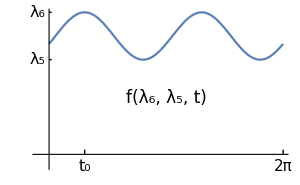

```mathematica
λ6=3;λ5=2;
Show[{Plot[ff[λ6,λ5,t],{t,0,2π},Ticks->None,AxesOrigin->{0,0}],
Graphics[{
Line[{{0,λ6},{.07,λ6}}],
Line[{{0,λ5},{.07,λ5}}],
Line[{{t0,0},{t0,.1}}],
Line[{{2π,0},{2π,.1}}],
Text[Style["f(λ_6, λ_5, t)",17],{π,.6λ5}],
Text[Style["λ_6",16],{-.3,λ6}],
Text[Style["λ_5",16],{-.3,λ5}],
Text[Style["t_0",16],{t0,-.25}],
Text[Style["2π",15],{2π,-.25}]}]},PlotRange->All,ImageSize->300]
```